Influence of the closing angle on the current peak in a simple R-L circuit

Definition of a circuit parameters

```mathematica
R = 5
L = 0.1
f = 50
XL = 2*Pi*f*L
fi = ArcTan[XL/R]
Cos[fi]
```

5

0.1

50

31.4159

1.41297

0.157177

Closing angle

```mathematica
alpha = 0
```

0

Voltage definition

```mathematica
U = 230
u[t_, alfa_] = Sqrt[2]*U*Sin[2*Pi*f*t+alfa]
```

230

230 √2 Sin[alfa+100 π t]

Current function computation
Case 1: DC Voltage

```mathematica
sol= DSolve[{i'[t] == 1/L*U - R/L*i[t], i[0]==0, i'[0]==U/L},i,t]
```

{{i→Function[{t},46. ⅇ^(-50. t) (-1.+1. ⅇ^(50. t))]}}

```mathematica
sol = sol[[1]]
```

{i→Function[{t},46. ⅇ^(-50. t) (-1.+1. ⅇ^(50. t))]}

```mathematica
U/R
```

46

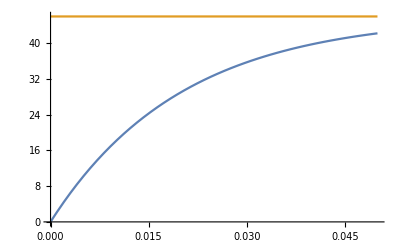

```mathematica
Plot[{46. ⅇ^(-50. t) (-1.+1. ⅇ^(50. t)),46 }, {t, 0, 0.05}]
```

Case 2: AC Voltage

```mathematica
sol2 = DSolve[{i'[t] == 1/L*u[t, alpha] - R/L*i[t], i[0]==0, i'[0]==u[0, alpha]/L},i,t]
```

{{i→Function[{t},-10.0979 ⅇ^(-50. t) ((-1.+2.74292×10^-17 ⅈ)+1. ⅇ^(50. t) Cos[314.159 t]-(0.159155-4.3655×10^-18 ⅈ) ⅇ^(50. t) Sin[314.159 t])]}}

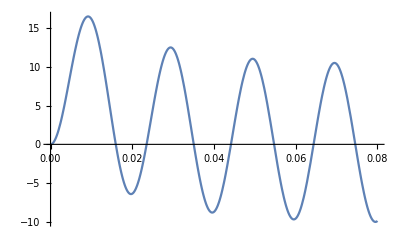

```mathematica
Plot[-10.097855956369427 ⅇ^(-50. t) ((-1.+2.7429242690887388*^-17 ⅈ)+1. ⅇ^(50. t) Cos[314.1592653589793 t]-(0.15915494309189532-4.365499559521968*^-18 ⅈ) ⅇ^(50. t) Sin[314.1592653589793 t]), {t, 0, 0.08}]
```

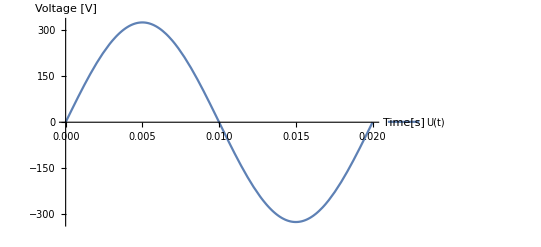

```mathematica
Plot[u[t, alpha], {t, 0, 0.02}, AxesLabel -> {"Time[s]", "Voltage [V]"},PlotLegends -> {"U(t)"}]
```

Time constant

```mathematica
L/R
```

0.02